### ComplexPlot

This package provides commands for visualizing complex-valued functions by generating two-dimensional QColorDensityGraphics, ContourGraphics and three dimensional SurfaceGraphics of complex-valued functions with a color code for complex numbers.

QComplexPlot3D[f[x,y],{x,xmin,xmax},{y,ymin,ymax},opts] | generates a surface plot of a complex-valued function f of two variables. The height of the surface is given by the absolute value, the color is determined by the complex value of f according to the option QComplexToColorMap. Package: VQM`ComplexPlot`.
QListComplexPlot3D[array,opts] |  generates a SurfaceGraphics from a two-dimensional array of complex numbers. The height of the surface is given by the absolute value, the color is determined by the complex value of f according to the option QComplexToColorMap. Package: VQM`ComplexPlot`.
QComplexSurfacePlot[f[x,y],{x,xmin,xmax},{y,ymin,ymax},opts] |  is similar to QListComplexPlot3D, but with a 'real surface look'. The option QHighlights->On (default) lets the surface appear glossy. Package: VQM`ComplexPlot`.
QListComplexSurfacePlot[array,opts] |  is similar to QListComplexPlot3D, but with a 'real surface look'. The option QHighlights->On (default) lets the surface appear glossy. Package: VQM`ComplexPlot`.
QComplexDensityPlot[f[x,y],{x,xmin,xmax},{y,ymin,ymax},opts] |  generates a QColorDensityGraphics of a complex-valued function f of two variables x and y. It is similar to DensityPlot. The complex value f[x,y] is mapped one-to-one to a color. The color map is given by the option QComplexToColorMap. The default $QComplexToColorMap determines the hue of the color from Arg[z], and the lightness from Abs[z]. Package: VQM`ComplexPlot`.
QSpinorDensityPlot[{f,g}, {x,xmin,xmax}, {y,ymin,ymax}, opts] |  visualizes a C^2-valued function in two dimensions by interlacing colored density plots of the components f and g. Each 'pixel' thus has an upper part with a color corresponding to the complex value of the upper component f, and a lower part with a color corresponding to the lower component g. Package: VQM`ComplexPlot`.
QListComplexDensityPlot[array,opts] |  gives a QColorDensityGraphics of a two-dimensional array of complex numbers. It is similar to ListDensityPlot. Each complex number is mapped one-to-one to a color. The color map is determinded by the option QComplexToColorMap. The default $QComplexToColorMap determines the hue of the color from Arg[z], and the lightness from Abs[z]. Package: VQM`ComplexPlot`.
QComplexContourPlot[f[x,y],{x,xmin,xmax},{y,ymin,ymax},opts] |  visualizes a complex-valued function f of two variables x and y. QComplexContourPlot combines a QColorDensityGraphics with a ContourGraphics of the absolute value of f. Package: VQM`ComplexPlot`.
QListComplexContourPlot[array,opts] |  generates a QColorDensityGraphics of a two-dimensional array of complex numbers and combines it with a ContourGraphics of Abs[array]. Package: VQM`ComplexPlot`.
QColorArrayPlot[list, opts] |  makes a 2D raster plot with colors given by list. Here list is a two-dimensional array of color directives. Package: VQM`ComplexPlot`.
QColorDensityGraphics[absarray,colorarray,{opts}] |  is a representation of a two-dimensional plot of an array of complex numbers. It can be converted to SurfaceGraphics, ContourGraphics, DensityGraphics and Graphics objects. Package: VQM`ComplexPlot`.

This loads the package

```mathematica
Needs["VQM`ComplexPlot`"]
```

This is an example

```mathematica
msgonindet=Head[General::"indet"]=!=$Off;
Off[Arg::"indet"];
```

```mathematica
QComplexDensityPlot[x+ⅈ y,{x,-4,4},{y,-4,4}]
```

-Graphics-

```mathematica
gr1=QComplexDensityPlot[Sin[x+ⅈ y],{x,-π,π},{y,-1,2.5},Mesh->False,PlotPoints->30]
```

-Graphics-

```mathematica
QComplexPlot3D[Sin[x + I y],{x,-Pi,Pi},{y,-1,2.5}]
```

-Graphics3D-

```mathematica
QComplexContourPlot[x+ⅈ y,{x,-4,4},{y,-4,4},QValueRange->{2,5},PlotRange->{0,3},Contours->5,ContourStyle->GrayLevel[0.5]]
```

-Graphics-

```mathematica
QComplexContourPlot[Zeta[x+ⅈ y],{x,-0.7,2.5},{y,-2,42},PlotPoints->{10,50},PlotRange->{-1.5,8},Contours->8,AspectRatio->5]
```

-Graphics-

```mathematica
myfunc[{y_,m_,c_}]:=Hue[-2 y,1-m,c];
collist=Table[myfunc[Mod[{x,x+y,x-y},1]],{y,0,1,1/20.},{x,0,1,1/20.}];
QColorArrayPlot[collist,Mesh->False]
```

-Graphics-

```mathematica
lis=Table[N[Tan[x+ⅈ y]],{y,-1.,1,0.1},{x,-N[π],π,N[π]/10}];
QListComplexDensityPlot[lis,MeshRange->{{-π,π},{-1,1}}]
```

-Graphics-

```mathematica
QComplexPlot3D[2 ⅇ^(-x^2-y^2-3 ⅈ x) Sin[x+ⅈ y],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
f[x_,y_]:=Which[Abs[x+ⅈ y]>1.1,Indeterminate,Abs[x+ⅈ y]>0.8,0,Abs[x+ⅈ y]>0.5,ComplexInfinity,True,DirectedInfinity[x+ⅈ y]];
```

```mathematica
msgoncfsa=Head[CompiledFunction::"cfsa"]=!=$Off;
msgonrealu=Head[Graphics::"realu"]=!=$Off;
Off[CompiledFunction::"cfsa",Graphics::"realu"];
```

```mathematica
QComplexDensityPlot[f[x,y],{x,-1,1},{y,-1,1},Compiled->False,QLightnessRange->{0.2,0.8}]
```

-Graphics-

```mathematica
QComplexDensityPlot[f[x,y],{x,-1,1},{y,-1,1},QValueChecking->Off,Compiled->False,QLightnessRange->{0.2,0.8}]
```

-Graphics-

```mathematica
If[msgoncfsa,On[CompiledFunction::"cfsa"]];
If[msgonrealu,On[Graphics::"realu"]];
```

```mathematica
arr=Table[ⅇ^(ⅈ 3 (x+y)-x^2-y^2)+ⅇ^(-ⅈ 2 (x+y)-(x-0.5)^2-(y-0.5)^2),{y,-3,3,0.1},{x,-3,3,0.1}];
QListComplexSurfacePlot[arr,PlotRange->All,QSphereRadius->0.5,QLightnessRange->{0.2,1.}]
```

-Graphics3D-

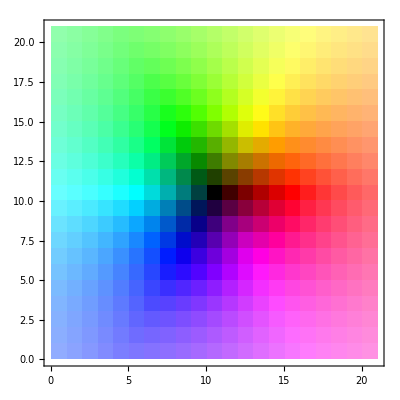

```mathematica
QColorArrayPlot[Table[QComplexToRGBColor[x+ⅈ y],{y,-2.,2,0.2},{x,-2.,2,0.2}],Mesh->False]
```

```mathematica
QSpinorDensityPlot[{ⅇ^(ⅈ x),ⅇ^(ⅈ y)},{x,-π,π},{y,-π,π},PlotPoints->20]
```

-Graphics-

```mathematica
If[msgonindet,On[Arg::"indet"]];
```